Utilities

```mathematica
Begin["frame`"];
CreateWindow@PaletteNotebook[{Button["Refresh",vars=Framed[Grid[Select[With[{expr=ToExpression@#},{Which[ListQ[expr],#,NumericQ[expr],#,True,expr],Head[expr],Which[ListQ[expr],Dimensions[expr],NumericQ[expr],expr,StringQ[expr],StringLength[expr],True,"-"]}]&/@Names["Global`*"],(#[[2]]=!=Framed)&],Alignment->Left],FrameStyle->None,FrameMargins->5]],Dynamic[vars]},WindowElements->{"VerticalScrollBar"},WindowTitle->"Global`*"];
End[];

$Post=If[ListQ[#],MatrixForm[#],#] &;

Button["Evaluate core Subroutines",NotebookLocate["CoreSubroutines"];
SelectionEvaluateCreateCell[EvaluationNotebook[]]]
```

Things to do:

1. Repeat in spherical co-ordinates
2. Stress feild
3. Work with explicit expression. 
4. Simplify for a complex three-dimensional field.

```mathematica
Off[Unset::norep];
Off[Remove::rmnsm];
DeleteCases[Names@{"Global`*","SphereRotation`*"},"complexsymbolsplt"];
ClearAll[#] & /@(%);
Remove[#] &/@(%%);
<<Notation`
RemoveSymbolize[Subscript[x_, 1]]
RemoveSymbolize[Subscript[x_, 2]]
RemoveSymbolize[Subscript[x_, 3]]
RemoveSymbolize[r^2]


Symbolize[Subscript[x_, 1]]
Symbolize[Subscript[x_, 2]]
Symbolize[Subscript[x_, 3]]
Symbolize[Subscript[x_, R]]
Symbolize[Subscript[x_, ϕ]]
Symbolize[Subscript[x_, θ]]

Symbolize[r^2]
(*Needs["ComplexSymbols`", URLDownload["https://www.dropbox.com/s/jilor1vs7b78tqh/ComplexSymbols.wl?raw=1"]]*)
Needs["ComplexSymbols`","/Users/haneeshkesari/Dropbox (Brown)/DropboxBrown/Code/WMath/ComplexSymbols.wl"]
complexsymbols=AssignLabels[{"e_1","e_2","e_3","u","∇u","u","∇u","ϵ","H","ϵ","σ","λ","μ"}]
NotebookClose[complexsymbolsplt];
complexsymbolsplt=SymbolPalette["Complex Symbols",complexsymbols,1];
```

{e_1,e_2,e_3,u,∇u,u,∇u,ϵ,H,ϵ,σ,λ,μ}

```mathematica
"Evaluate core Subroutines"
```

Core Subroutines

```mathematica
ClearAll[Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]]
{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]}
Begin["SphereRotation`"];
SphereRotation`μ::usage="Shear modulus";
SphereRotation`λ::usage="lame constnat";
SphereRotation`ρ::usage="The sphere's density";
SphereRotation`a::usage="The sphere's density";
SphereRotation`ω::usage="The sphere's angular velocity";
Subscript[u, 1]::usage="Displacement component in the StyleBox[SubscriptBox[StyleBox["e",FontFamily->"Times",FontSize->14,FontWeight->"Bold"], StyleBox["1",FontSize->9.9399995803833,FontWeight->"Regular"]],FontFamily->"Times",FontSize->14,FontWeight->"Bold"] direction";
Subscript[u, 2]::usage="Displacement component in the e_2 direction";
Subscript[u, 3]::usage="Displacement component in the SubscriptBox[StyleBox["e",FontFamily->"Times New Roman",FontSize->14,FontWeight->"Bold"], "3"] direction";

With[{opts=OptionsPattern[{SphereRotation`λ->Global`λ,SphereRotation`μ->Global`μ,SphereRotation`ρ->Global`ρ,SphereRotation`ω->Global`ω,SphereRotation`a->Global`a}],inits=x},

Subscript[u, 1][Subscript[x, 1]:_,Subscript[x, 2]:_,Subscript[x, 3]:_,opts]:=Module[{r^2=Subscript[x, 1]^2+Subscript[x, 2]^2+Subscript[x, 3]^2,
																		λ=OptionValue[SphereRotation`λ],
																		μ=OptionValue[SphereRotation`μ],
																		ρ=OptionValue[SphereRotation`ρ],
																		ω=OptionValue[SphereRotation`ω],
																		a=OptionValue[SphereRotation`a]},
					Subscript[x, 1] (ρ ω^2)/3(
							1/(5(λ+2μ))((5λ+6μ)/(3λ+2μ)a^2-r^2)+
							1/(μ (19λ+14μ))(
										(4λ+3μ)a^2+
										-1/2(5λ+4μ)r^2+
										(λ+μ)(Subscript[x, 1]^2+Subscript[x, 2]^2-2 Subscript[x, 3]^2)
										)
						)];



Subscript[u, 2][Subscript[x, 1]:_,Subscript[x, 2]:_,Subscript[x, 3]:_,opts]:=Module[{r^2=Subscript[x, 1]^2+Subscript[x, 2]^2+Subscript[x, 3]^2,
																		λ=OptionValue[SphereRotation`λ],
																		μ=OptionValue[SphereRotation`μ],
																		ρ=OptionValue[SphereRotation`ρ],
																		ω=OptionValue[SphereRotation`ω],
																		a=OptionValue[SphereRotation`a]},
					Subscript[x, 2] (ρ ω^2)/3(
							1/(5(λ+2μ))((5λ+6μ)/(3λ+2μ)a^2-r^2)+
							1/(μ (19λ+14μ))(
										(4λ+3μ)a^2+
										-1/2(5λ+4μ)r^2+
										(λ+μ)(Subscript[x, 1]^2+Subscript[x, 2]^2-2 Subscript[x, 3]^2)
										)
						)];




Subscript[u, 3][Subscript[x, 1]:_,Subscript[x, 2]:_,Subscript[x, 3]:_,opts]:=Module[{r^2=Subscript[x, 1]^2+Subscript[x, 2]^2+Subscript[x, 3]^2,
																		λ=OptionValue[SphereRotation`λ],
																		μ=OptionValue[SphereRotation`μ],
																		ρ=OptionValue[SphereRotation`ρ],
																		ω=OptionValue[SphereRotation`ω],
																		a=OptionValue[SphereRotation`a]},

					Subscript[x, 3] (ρ ω^2)/3(
						
						1/(5(λ+2μ))((5λ+6μ)/(3λ+2μ)a^2-r^2)+
						1/(μ (19λ+14μ))(
									-(8λ+6μ)a^2+
									(5λ+4μ)r^2+
									(λ+μ)(Subscript[x, 1]^2+Subscript[x, 2]^2-2 Subscript[x, 3]^2)
									)
						)
];
]
End[];
```

{u_1,u_2,u_3}

Numerical

```mathematica
ClearAll["u"]
ClearAll[ω]
Block[{𝓍,𝓎,𝓏,ℓ,𝓂,
λ=Quantity[22,"Pascals"],
μ=Quantity[11,"Pascals"],
ρ=Quantity[1,"Grams"]/Quantity[1,"Centimeter"]^3,
ω=25/Quantity[1,"second"],
𝒶=15,
a=Quantity[𝒶,"Centimeters"],
x=Quantity[𝓍,"Centimeters"],
y=Quantity[𝓎,"Centimeters"],
z=Quantity[𝓏,"Centimeters"]
},

"u"[𝓍_,𝓎_,𝓏_]={Subscript[u, 1][x,y,z,SphereRotation`ω->Evaluate@ω,SphereRotation`ρ->ρ,SphereRotation`λ->Evaluate@λ,SphereRotation`μ->Evaluate@μ,SphereRotation`a->a],Subscript[u, 2][x,y,z,SphereRotation`ω->ω,SphereRotation`ρ->ρ,SphereRotation`λ->λ,SphereRotation`μ->μ,SphereRotation`a->a],Subscript[u, 3][x,y,z,SphereRotation`ω->ω,SphereRotation`ρ->ρ,SphereRotation`λ->λ,SphereRotation`μ->μ,SphereRotation`a->a]};

"∇u"[𝓍_,𝓎_,𝓏_]=Grad["u"[𝓍,𝓎,𝓏],{𝓍,𝓎,𝓏}];
"ϵ"[𝓍_,𝓎_,𝓏_]=Evaluate[("∇u"[𝓍,𝓎,𝓏]+Transpose["∇u"[𝓍,𝓎,𝓏]])];
]
```

```mathematica
"ϵ"[x,y,z][[1,2]]//Simplify
"ϵ"[x,y,z][[2,3]]//Simplify
"ϵ"[x,y,z][[1,3]]//Simplify
"ϵ"[x,y,z]//Tr//Simplify
```

```mathematica
Block[{𝒶=15},
{ContourPlot3D[{"ϵ"[x,y,z][[1,2]]//QuantityMagnitude},{x,-1.2𝒶,1.2𝒶},{y,-1.2𝒶,1.2𝒶},{z,-1.2𝒶,1.2𝒶},RegionFunction->Function[{x,y,z},x^2+y^2+z^2≤ 𝒶^2],Mesh->True,Contours->10,ContourStyle->Directive[Orange,Opacity[0.1],Specularity[White,30]]],
ContourPlot3D[{"ϵ"[x,y,z][[1,3]]//QuantityMagnitude},{x,-1.2𝒶,1.2𝒶},{y,-1.2𝒶,1.2𝒶},{z,-1.2𝒶,1.2𝒶},RegionFunction->Function[{x,y,z},x^2+y^2+z^2≤ 𝒶^2],Mesh->True,Contours->10,ContourStyle->Directive[Orange,Opacity[0.1],Specularity[White,30]]]}
]
```

```mathematica
"u"[x_,y_,z_]={Subscript[u, 1][x,y,z],Subscript[u, 2][x,y,z],Subscript[u, 3][x,y,z]};
"∇u"[𝓍_,𝓎_,𝓏_]=Grad["u"[𝓍,𝓎,𝓏],{𝓍,𝓎,𝓏}];
"ϵ"[𝓍_,𝓎_,𝓏_]=1/2(("∇u"[𝓍,𝓎,𝓏]+Transpose["∇u"[𝓍,𝓎,𝓏]]));
"ϵ"[x,y,z][[1,2]]//Simplify
"ϵ"[x,y,z][[2,3]]//Simplify
"ϵ"[x,y,z][[1,3]]//Simplify
"ϵ"[x,y,z]//Tr//Simplify
```

-(x y (5 λ^2+26 λ μ+16 μ^2) ρ ω^2)/(5 μ (λ+2 μ) (19 λ+14 μ))

-(y z (-5 λ^2+12 λ μ+12 μ^2) ρ ω^2)/(10 μ (λ+2 μ) (19 λ+14 μ))

-(x z (-5 λ^2+12 λ μ+12 μ^2) ρ ω^2)/(10 μ (λ+2 μ) (19 λ+14 μ))

((a^2 (95 λ^2+184 λ μ+84 μ^2)-5 (3 λ+2 μ) (x^2 (6 λ+4 μ)+y^2 (6 λ+4 μ)+z^2 (7 λ+6 μ))) ρ ω^2)/(5 (λ+2 μ) (3 λ+2 μ) (19 λ+14 μ))

```mathematica
Subscript[e, 1]={1,0,0};
Subscript[e, 2]={0,1,0};
Subscript[e, 3]={0,0,1};
Subscript[g, 1]=Subscript[e, 3];
Subscript[Q, 1]=RotationMatrix[θ,Subscript[g, 1]];
Subscript[g, 2]=Subscript[Q, 1].Subscript[e, 2];
Subscript[Q, 2]=RotationMatrix[ϕ,Subscript[g, 2]];
Q=Subscript[Q, 2].Subscript[Q, 1];
```

```mathematica
Q;
%//.Conjugate[x_]->x;
%//.Abs[x_]->x;
Set[Q,%//Simplify];
(Subscript[e, R]=Subscript[f, 3]=Q.Subscript[e, 3]);
Echo[%//MatrixForm,"e_R ="];
(Subscript[e, ϕ]=Subscript[f, 1]=Q.Subscript[e, 1]);
Echo[%//MatrixForm,"e_ϕ ="];
(Subscript[e, θ]=Subscript[f, 2]=Q.Subscript[e, 2]);
Echo[%//MatrixForm,"e_θ ="];
(* from MathWorld*)
```

e_R = (Cos[θ] Sin[ϕ]
Sin[θ] Sin[ϕ]
Cos[ϕ])

e_ϕ = (Cos[θ] Cos[ϕ]
Cos[ϕ] Sin[θ]
-Sin[ϕ])

e_θ = (-Sin[θ]
Cos[θ]
0)

```mathematica
ClearAll[Subscript[u, R],Subscript[u, ϕ],Subscript[u, θ]];
dummy="u"@@(R Subscript[e, R])//Simplify;
Subscript[u, R][R_,ϕ_,θ_]=(dummy.Subscript[e, R])//Simplify;
Subscript[u, ϕ][R_,ϕ_,θ_]=(dummy.Subscript[e, ϕ])//Simplify
Subscript[u, θ][R_,ϕ_,θ_]=(dummy.Subscript[e, θ])//Simplify
```

(R (-R^2 (5 λ+4 μ)+a^2 (8 λ+6 μ)) ρ ω^2 Sin[2 ϕ])/(4 μ (19 λ+14 μ))

0

```mathematica
ClearAll["u"];
"u"[R_,ϕ_,θ_]={Subscript[u, R][R,ϕ,θ],Subscript[u, ϕ][R,ϕ,θ],Subscript[u, θ][R,ϕ,θ]}
```

{(R ρ ω^2 (-2 a^2 (20 λ^3+5 λ^2 μ-56 λ μ^2-36 μ^3)+R^2 (15 λ^3-26 λ^2 μ-60 λ μ^2-24 μ^3)-5 (3 λ^2+8 λ μ+4 μ^2) (-R^2 (3 λ+2 μ)+a^2 (8 λ+6 μ)) Cos[2 ϕ]))/(20 μ (λ+2 μ) (3 λ+2 μ) (19 λ+14 μ)),(R (-R^2 (5 λ+4 μ)+a^2 (8 λ+6 μ)) ρ ω^2 Sin[2 ϕ])/(4 μ (19 λ+14 μ)),0}

```mathematica
(LHS="u"[m,n,o]//Simplify)//MatrixForm
```

((m ρ ω^2 (-2 a^2 (20 λ^3+5 λ^2 μ-56 λ μ^2-36 μ^3)+m^2 (15 λ^3-26 λ^2 μ-60 λ μ^2-24 μ^3)-5 (3 λ^2+8 λ μ+4 μ^2) (-m^2 (3 λ+2 μ)+a^2 (8 λ+6 μ)) Cos[2 n]))/(20 μ (λ+2 μ) (3 λ+2 μ) (19 λ+14 μ))
(m (-m^2 (5 λ+4 μ)+a^2 (8 λ+6 μ)) ρ ω^2 Sin[2 n])/(4 μ (19 λ+14 μ))
0)

```mathematica
(RHS=TransformedField["Cartesian"->"Spherical","u"[x,y,z], {x,y,z}->{m,n,o}]//Simplify)//MatrixForm
```

((m ρ ω^2 (-2 a^2 (20 λ^3+5 λ^2 μ-56 λ μ^2-36 μ^3)+m^2 (15 λ^3-26 λ^2 μ-60 λ μ^2-24 μ^3)-5 (3 λ^2+8 λ μ+4 μ^2) (-m^2 (3 λ+2 μ)+a^2 (8 λ+6 μ)) Cos[2 n]))/(20 μ (λ+2 μ) (3 λ+2 μ) (19 λ+14 μ))
(m (-m^2 (5 λ+4 μ)+a^2 (8 λ+6 μ)) ρ ω^2 Sin[2 n])/(4 μ (19 λ+14 μ))
0)

```mathematica
("∇u"[R_,ϕ_,θ_]=Grad["u"[R,ϕ,θ],{R,ϕ,θ},"Spherical"]//Simplify)
```

{{-(ρ ω^2 (2 a^2 (20 λ^3+5 λ^2 μ-56 λ μ^2-36 μ^3)+3 R^2 (-15 λ^3+26 λ^2 μ+60 λ μ^2+24 μ^3)+5 (3 λ^2+8 λ μ+4 μ^2) (-3 R^2 (3 λ+2 μ)+a^2 (8 λ+6 μ)) Cos[2 ϕ]))/(20 μ (λ+2 μ) (3 λ+2 μ) (19 λ+14 μ)),((-R^2 λ+a^2 (8 λ+6 μ)) ρ ω^2 Sin[2 ϕ])/(4 μ (19 λ+14 μ)),0},{((-3 R^2 (5 λ+4 μ)+a^2 (8 λ+6 μ)) ρ ω^2 Sin[2 ϕ])/(4 μ (19 λ+14 μ)),(ρ ω^2 (-2 a^2 (20 λ^3+5 λ^2 μ-56 λ μ^2-36 μ^3)+R^2 (15 λ^3-26 λ^2 μ-60 λ μ^2-24 μ^3)+5 (3 λ^2+8 λ μ+4 μ^2) (-R^2 (7 λ+6 μ)+a^2 (8 λ+6 μ)) Cos[2 ϕ]))/(20 μ (λ+2 μ) (3 λ+2 μ) (19 λ+14 μ)),0},{0,0,(ρ ω^2 (8 a^2 (5 λ^3+25 λ^2 μ+32 λ μ^2+12 μ^3)-R^2 (30 λ^3+143 λ^2 μ+160 λ μ^2+52 μ^3)-5 R^2 (3 λ^3+11 λ^2 μ+12 λ μ^2+4 μ^3) Cos[2 ϕ]))/(10 μ (λ+2 μ) (3 λ+2 μ) (19 λ+14 μ))}}

Old

```mathematica
ClearAll[Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]]
{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]}
Begin["SphereRotation`"];
SphereRotation`μ::usage="Shear modulus";
SphereRotation`λ::usage="lame constnat";
SphereRotation`ρ::usage="The sphere's density";
SphereRotation`a::usage="The sphere's density";
SphereRotation`ω::usage="The sphere's angular velocity";
Subscript[u, 1]::usage="Displacement component in the StyleBox[SubscriptBox[StyleBox["e",FontFamily->"Times",FontSize->14,FontWeight->"Bold"], StyleBox["1",FontSize->9.9399995803833,FontWeight->"Regular"]],FontFamily->"Times",FontSize->14,FontWeight->"Bold"] direction";
Subscript[u, 2]::usage="Displacement component in the e_2 direction";
Subscript[u, 3]::usage="Displacement component in the SubscriptBox[StyleBox["e",FontFamily->"Times New Roman",FontSize->14,FontWeight->"Bold"], "3"] direction";

With[{opts=OptionsPattern[{SphereRotation`λ->Global`λ,SphereRotation`μ->Global`μ,SphereRotation`ρ->Global`ρ,SphereRotation`ω->Global`ω,SphereRotation`a->Global`a}],inits=x},

Subscript[u, 1][Subscript[x, 1]:_,Subscript[x, 2]:_,Subscript[x, 3]:_,opts]:=Module[{r^2=Subscript[x, 1]^2+Subscript[x, 2]^2+Subscript[x, 3]^2,
																		λ=OptionValue[SphereRotation`λ],
																		μ=OptionValue[SphereRotation`μ],
																		ρ=OptionValue[SphereRotation`ρ],
																		ω=OptionValue[SphereRotation`ω],
																		a=OptionValue[SphereRotation`a]},
					Subscript[x, 1] (ρ ω^2)/3(
							1/(5(λ+2μ))((5λ+6μ)/(3λ+2μ)a^2-r^2)+
							1/(μ (19λ+14μ))(
										(4λ+3μ)a^2+
										-1/2(5λ+4μ)r^2+
										(λ+μ)(Subscript[x, 1]^2+Subscript[x, 2]^2-2 Subscript[x, 3]^2)
										)
						)];



Subscript[u, 2][Subscript[x, 1]:_,Subscript[x, 2]:_,Subscript[x, 3]:_,opts]:=Module[{r^2=Subscript[x, 1]^2+Subscript[x, 2]^2+Subscript[x, 3]^2,
																		λ=OptionValue[SphereRotation`λ],
																		μ=OptionValue[SphereRotation`μ],
																		ρ=OptionValue[SphereRotation`ρ],
																		ω=OptionValue[SphereRotation`ω],
																		a=OptionValue[SphereRotation`a]},
					Subscript[x, 2] (ρ ω^2)/3(
							1/(5(λ+2μ))((5λ+6μ)/(3λ+2μ)a^2-r^2)+
							1/(μ (19λ+14μ))(
										(4λ+3μ)a^2+
										-1/2(5λ+4μ)r^2+
										(λ+μ)(Subscript[x, 1]^2+Subscript[x, 2]^2-2 Subscript[x, 3]^2)
										)
						)];




Subscript[u, 3][Subscript[x, 1]:_,Subscript[x, 2]:_,Subscript[x, 3]:_,opts]:=Module[{r^2=Subscript[x, 1]^2+Subscript[x, 2]^2+Subscript[x, 3]^2,
																		λ=OptionValue[SphereRotation`λ],
																		μ=OptionValue[SphereRotation`μ],
																		ρ=OptionValue[SphereRotation`ρ],
																		ω=OptionValue[SphereRotation`ω],
																		a=OptionValue[SphereRotation`a]},

					Subscript[x, 3] (ρ ω^2)/3(
						
						1/(5(λ+2μ))((5λ+6μ)/(3λ+2μ)a^2-r^2)+
						1/(μ (19λ+14μ))(
									-(8λ+6μ)a^2+
									(5λ+4μ)r^2+
									(λ+μ)(Subscript[x, 1]^2+Subscript[x, 2]^2-2 Subscript[x, 3]^2)
									)
						)
];
]
End[];
```

```mathematica
(*AppendTo[$ContextPath,"SphereRotation`"];
$ContextPath=DeleteDuplicates[$ContextPath];
*)
```

```mathematica
<<HaneeshPackages`
```

```mathematica
"ϵ"[R_,ϕ_,θ_]=(("∇u"[R,ϕ,θ]+"∇u"[R,ϕ,θ]ᵀ)/2//Simplify);
```

```mathematica
Block[{λ=(Ε ν)/((1+ν)(1-2ν)),μ=Ε/(2(1+ν)),dummy},
dummy={"ϵ"[a,π/2,θ][[3,3]],"ϵ"[0,π/4,θ][[1,2]]}//Simplify;
dummy/.ν->1/2//N

(*"ϵ"[0,π/4,θ][[1,2]]*)]
```

{(0.131579 a^2 ρ ω^2)/Ε,(0.315789 a^2 ρ ω^2)/Ε}

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(a^2 (4 ) ρ ω^2)/(2 μ (19 ))//N
```

(0.105263 a^2 ρ ω^2)/μ

```mathematica
(a^2 (25 ) ρ ω^2)/(10 μ (57))//N
```

(0.0438596 a^2 ρ ω^2)/μ

```mathematica
Expand[(3 λ+2 μ) (19 λ+14 μ)]
```

```mathematica
-(a^2 (-8+ν+5 ν^2) ρ ω^2)/(5 Ε (7+5 ν))/.ν->1/2//N
```

(0.131579 a^2 ρ ω^2)/Ε

```mathematica
0.043859649122807015 *3
```

0.131579

```mathematica
"ϵ"[R,ϕ,θ][[1,2]]//FullSimplify
```

((a-R) (a+R) (4 λ+3 μ) ρ ω^2 Cos[ϕ] Sin[ϕ])/(μ (19 λ+14 μ))

```mathematica
"u"[R,ϕ,θ]//Simplify//MatrixForm
```

((R ρ ω^2 (-2 a^2 (20 λ^3+5 λ^2 μ-56 λ μ^2-36 μ^3)+R^2 (15 λ^3-26 λ^2 μ-60 λ μ^2-24 μ^3)-5 (3 λ^2+8 λ μ+4 μ^2) (-R^2 (3 λ+2 μ)+a^2 (8 λ+6 μ)) Cos[2 ϕ]))/(20 μ (λ+2 μ) (3 λ+2 μ) (19 λ+14 μ))
(R (-R^2 (5 λ+4 μ)+a^2 (8 λ+6 μ)) ρ ω^2 Sin[2 ϕ])/(4 μ (19 λ+14 μ))
0)

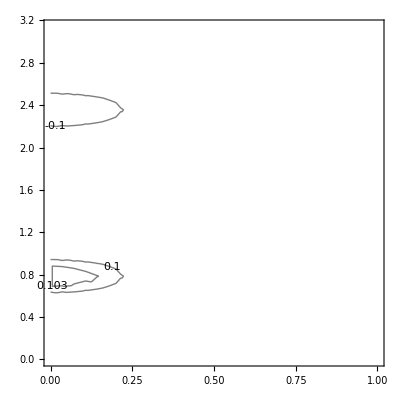

```mathematica
Block[{a=1,ρ=1,ω=1,μ=1,λ=100000},
ContourPlot["ϵ"[R,ϕ,θ][[1,2]]//N,{R,0,1},{ϕ,0,π},ContourLabels->True,ContourStyle->Black,ContourShading->False,Contours->{-0.1,0.1,0.103,-0.2}]
]
```

```mathematica
3π/4//N
```

2.35619